```mathematica
dergen = Flatten[Import["~/zeca-results-all-cell/zeca-results-all-cell/Top8000-best_hom50_pdb_chain/rose_special_charged/run_10000/deriva_genetica_occ"]];
```

```mathematica
occ = Counts[dergen];
pre = Table[0, Range[563]];
```

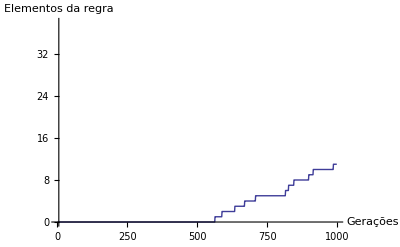

```mathematica
plotDG = ListLinePlot[Join[pre,Values[occ]], PlotRange-> {{1,1000},{0,38}}, PlotTheme->"Classic", AxesLabel->{"Gerações", "Elementos da regra"}]
```

```mathematica
Export["~/Documentos/PhD-Quali/latex/quali/figures/deriva_genetica.pdf", plotDG]
```

~/Documentos/PhD-Quali/latex/quali/figures/deriva_genetica.pdf